```mathematica
Begin["BoatContext`"];
libboatLocation="/home/wolf/qea/libboat.nb";
libboat=NotebookOpen[libboatLocation];
SelectionMove[libboat,All,Notebook];
SelectionEvaluate[libboat];
Needs["CUDALink`"];
```

```mathematica
bHullLocation="/home/wolf/qea/bhull.stl";
hullLocation="/home/wolf/qea/hull.stl";

bHullLocation="/home/wolf/qea/hulls/boats/boatfixed.stl";
hullLocation="/home/wolf/qea/hulls/boats/boatfixed.stl";

canLocation="/home/wolf/qea/can.stl";
can=Import[canLocation,"BoundaryMeshRegion"];

(* Convert from STL file units to cm *)
stlUnits="Meters";
stlScale=QuantityMagnitude[UnitConvert[stlUnits,Quantity[, "Centimeters"]]];

(* Generate point cloud *)
buoyHullNonScaled=Import[bHullLocation,"BoundaryMeshRegion"];
buoyHull=TransformedRegion[buoyHullNonScaled,ScalingTransform[{stlScale,stlScale,stlScale}]];
(*buoyHull=Import["/home/wolf/qea/hulls/cube/cube.stl","BoundaryMeshRegion"];*)
buoyHullVolume=Volume[buoyHull]Quantity[, ("Centimeters")^3];
buoyHullPoints=pointCloud[buoyHull,100000];

hullNonScaled=Import[hullLocation,"BoundaryMeshRegion"];
hull=TransformedRegion[hullNonScaled,ScalingTransform[{stlScale,stlScale,stlScale}]];
(*hull=Import["/home/wolf/qea/hulls/cube/cube.stl","BoundaryMeshRegion"];*)
hullVolume=Volume[buoyHull]Quantity[, ("Centimeters")^3];
hullCentroid=RegionCentroid[hull];

(* Constants *)
(*GeogravityModelData[CityData[Entity["City",{"Needham","Massachusetts","UnitedStates"}],"Coordinates"],"Magnitude"];*)
g=9.81 Quantity[, ("Meters")/("Seconds")^2];
blueFoamDensity=0.0317 Quantity[, ("Grams")/("Centimeters")^3];
waterDensity=1 Quantity[, ("Grams")/("Centimeters")^3];
```

```mathematica
can1Loc={0,4.5-2,9.35};
can2Loc={0,4.5-2,26};
frontVec=Normalize[{0,0,1}];
boat={
<|
name->"BuoyHull",
type->"Buoy",
mass->buoyHullVolume*waterDensity,
volume->buoyHullVolume,
points->buoyHullPoints,
front->frontVec,
render->{GraphicsComplex[MeshCoordinates@buoyHull,MeshCells[buoyHull,2]]},
cobRender->({White,PointSize[Large],Point[#]}&)
|>,
<|
name->"Hull",
type->"PointMass",
mass->hullVolume*blueFoamDensity,
volume->hullVolume,
com->Quantity[hullCentroid,"Centimeters"],
render->{
{Black,PointSize[Large],Point[hullCentroid]},
{EdgeForm[],Opacity[.6],LightPink,GraphicsComplex[MeshCoordinates@hull,MeshCells[hull,2]]}
}
|>,
<|
name->"Can",
type->"PointMass",
mass->389.5 Quantity[, "Grams"],
volume->Quantity[, "USSodaCanVolumes"],
com->Quantity[can1Loc,"Centimeters"],
render->{
{Brown,PointSize[Large],Point[can1Loc]},
{EdgeForm[],Opacity[.6],LightGray,Translate[GraphicsComplex[MeshCoordinates@can,MeshCells[can,2]],can1Loc]}
}
|>,
<|
name->"Can",
type->"PointMass",
mass->389.5 Quantity[, "Grams"],
volume->Quantity[, "USSodaCanVolumes"],
com->Quantity[can2Loc,"Centimeters"],
render->{
{LightBrown,PointSize[Large],Point[can2Loc]},
{EdgeForm[],Opacity[.6],LightGray,Translate[GraphicsComplex[MeshCoordinates@can,MeshCells[can,2]],can1Loc]}
}
|>
};
renderBoatWithForces[boat,Normalize[{0,1,0}]]

(*,{can1X,0,20},{can1Y,0,20},
ContinuousAction->False]*)
```

-Graphics3D-

## Boats

```mathematica
calculateMoments[boat,Normalize[{0,1,0}]]
```

{{-1.32889×10^7 g cm^2/s^2,0. g cm^2/s^2,-4767.68 g cm^2/s^2},{605853. g cm^2/s^2,0. g cm^2/s^2,34.7285 g cm^2/s^2},{-382100. g cm^2/s^2,0. g cm^2/s^2,0. g cm^2/s^2},{382100. g cm^2/s^2,0. g cm^2/s^2,0. g cm^2/s^2}}

```mathematica
renderBoatWithForces[boat,Normalize[{0,1,0}]]
```

-Graphics3D-

```mathematica
rightingArm[boat,Normalize[{-1,0,0}]]
```

-0.689989 cm

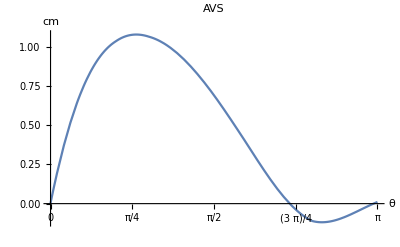

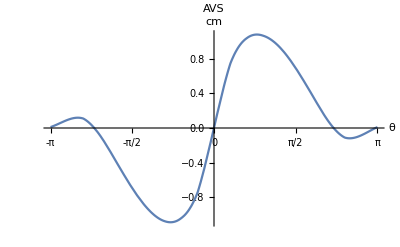

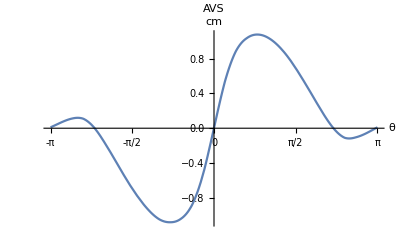

```mathematica
DistributeDefinitions["BoatContext`"];
plotAVS[boat,10,{0,Pi}]
plotCircleAVS[boat,20]
plotCircleAVS[boat,30]
```

```mathematica
manyBoats[boat,10]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}